```mathematica
(* Metric *)
gcov=DiagonalMatrix[{-(1-2/r),r/(r-2),r^2,r^2 Sin[theta]^2}];
gcon=FullSimplify[Inverse[gcov]];
MatrixForm[gcov]
MatrixForm[gcon]

(* Boosts vector au from the frame moving at velocity wu to frame moving at velocity uu *)
LorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{lorentzgam,Omeg,OmegSq,Lam},lorentzgam=-wu.ud;Omeg=Table[uu[[mu]]wd[[nu]]-wu[[mu]]ud[[nu]],{mu,1,4},{nu,1,4}]//.consts;OmegSq=Table[Sum[Omeg[[mu,sigma]]Omeg[[sigma,nu]],{sigma,1,4}],{mu,1,4},{nu,1,4}];Lam=IdentityMatrix[4]+OmegSq/(lorentzgam+1)+Omeg;Lam.au];
InverseLorentzBoostUpper[au_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostUpper[au,neguu,negud,wu,wd]];

InverseLorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=Block[{neguu,negud},neguu=-uu; neguu[[1]]=-neguu[[1]];negud=-ud; negud[[1]]=-negud[[1]];LorentzBoostLower[ad,neguu,negud,wu,wd]];

LorentzBoostLower[ad_,uu_,ud_,wu_,wd_]:=LorentzBoostUpper[ad,ud,uu,wd,wu];

vel3p2vel3u[vel3phys_]:={1,Sqrt[gcon[[2,2]]]Sqrt[-gcov[[1,1]]] vel3phys[[2]],Sqrt[gcon[[3,3]]] Sqrt[-gcov[[1,1]]]vel3phys[[3]],Sqrt[gcon[[4,4]]]Sqrt[-gcov[[1,1]]] vel3phys[[4]]};

vel3u2vel4u[vel3u_]:=Block[{uut},uut=1/(-gcov[[1,1]]-Sum[gcov[[i,i]] vel3u[[i]]^2,{i,2,4}])^(1/2); vel3u uut];

vel3p2vel4u[vel3phys_]:=vel3u2vel4u[vel3p2vel3u[vel3phys]];
```

(-1+2/r | 0 | 0 | 0
0 | r/(-2+r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[theta]^2)

(r/(2-r) | 0 | 0 | 0
0 | (-2+r)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[theta]^2/r^2)

```mathematica
FullSimplify[Det[gcov]]
```

-r^4 Sin[theta]^2

```mathematica
(* Setup fluid equations *)
```

```mathematica
Clear[ut,vp]
consts={gam->5/3,u->0.5``30,rho->0.1``30,r->6.0``30,theta->Pi/2,phi->0.0``30}
(*uu=ut{1,-0.1,0,  1/r^(3/2)}/.consts*) (* Kepler motion in phi, small radial velocity in r *)
(*uu={ut,-0.0,0, 0/r^(3/2)}/.consts*) (* Kepler motion in phi, small radial velocity in r *)
uu=ut{1,0.57``30,1.0``30*10^(-30),1/r^(3/2)}//.consts
ud=Table[Sum[gcov[[ii,jj]]*uu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
sol=Solve[Sum[uu[[ii]]ud[[ii]],{ii,1,4}]==-1,ut];
ut=ut/.sol[[2]]

wu={1/Sqrt[-gcov[[1,1]]] ,0,0,0}//.consts;
wd=Table[Sum[gcov[[ii,jj]]*wu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
lorentzgam=-wu.ud//.consts;

bsq0=5*2*(gam-1)*u//.consts
bflu={0,-0.00703939177500395``30,6.04549046091683``30*10^(-06),0.00687905349136715``30}
(*bflu={0,-0.001,0,-0.006}*)
(*bflu={0,-0.001,10^(-06),-0.001}*)
bfld=Table[Sum[gcov[[ii,jj]]*bflu[[ii]],{ii,1,4}],{jj,1,4}]//.consts
bflsq=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]
bflu=bflu*Sqrt[bsq0/bflsq]
bfld=bfld*Sqrt[bsq0/bflsq]
bflsqnew=Sum[bflu[[ii]]*bfld[[ii]],{ii,1,4}]


(* Boost back into Lab frame *)
bu=InverseLorentzBoostUpper[bflu,uu,ud,wu,wd]
bd=InverseLorentzBoostLower[bfld,uu,ud,wu,wd];

p=(gam-1)*u//.consts
WW=rho+u+p//.consts
bsq=Sum[bu[[i]]*bu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts
EF=(bsq+WW)//.consts
cs2=gam*p/WW//.consts
va2=bsq/EF//.consts
cms2=(va2+cs2*(1-va2))
```

{gam→5/3,u→0.5,rho→0.1,r→6.,theta→π/2,phi→0.}

{ut,0.57 ut,1.×10^-30 ut,0.0680413817439771693943690020752 ut}

{-0.6666666666666666666666666666667 ut,0.855 ut,3.6×10^-29 ut,2.44948974278317809819728407471 ut}

8.89108448948774112176643459

3.3333333333333333333333333333

{0,-0.00703939177500395,6.04549046091683×10^-6,0.00687905349136715}

{0,-0.010559087662505925,0.00021763765659300588,0.2476459256892174}

0.0017779004403046275001846563

{0,-0.30480409001239577943175152,0.00026176838532578185918952437,0.297861478178856111270053714}

{0,-0.45720613501859366914762728,0.00942366187172814693082287733,10.7230132144388200057219337}

3.33333333333333333333333333

{5.1070988494505574188154268,2.2537957119053338247543859,0.000261768385325781859189524375,0.60328369897245016196681488}

0.33333333333333333333333333333

0.93333333333333333333333333333

3.333333333333333333333333

4.266666666666666666666667

0.59523809523809523809523809524

0.78125

0.911458333333333333333333

```mathematica
ut
```

8.89108448948774112176643459

```mathematica
(* Boost bu to the fluid frame *)
bflu1=LorentzBoostUpper[bu,uu,ud,wu,wd]
bflu
bfld1=LorentzBoostLower[bd,uu,ud,wu,wd]
bfld
bu.bd
bflu.bfld
bflu1.bfld1
```

{0.,-0.304804090012395779431752,0.00026176838532578185918952437,0.2978614781788561112700537}

{0,-0.30480409001239577943175152,0.00026176838532578185918952437,0.297861478178856111270053714}

{0.,-0.457206135018593669147627,0.00942366187172814693082287733,10.72301321443882000572193}

{0,-0.45720613501859366914762728,0.00942366187172814693082287733,10.7230132144388200057219337}

3.333333333333333333333333

3.33333333333333333333333333

3.33333333333333333333333

```mathematica
(*Clear[bsq,va2,cs2,bu,bd,ku,kd,Kd,Ku,uu,ud,EF,WW,p,cm2]*)
```

```mathematica
(* Setup wave *)
```

```mathematica
kd=k*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[4,4]]]}/.consts
ku=Table[Sum[gcon[[ii,jj]]*kd[[ii]],{ii,1,4}],{jj,1,4}]//.consts
wfl=-(kd.uu)//.consts
ksq=(kd.ku+wfl^2)//.consts
kdotva=kd.bu/Sqrt[EF]//.consts
kdotva2=kdotva^2
FullSimplify[Sum[bu[[i]]*uu[[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]]//.consts
```

{-0.816496580927726032732428024902 k vphase,1.22474487139158904909864203735 k Cos[alpha],0,6. k Sin[alpha]}

{1.22474487139158904909864203735 k vphase,0.816496580927726032732428024902 k Cos[alpha],0,0.166666666666666666666666666667 k Sin[alpha]}

7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha]

-1. k^2 vphase^2+1. k^2 Cos[alpha]^2+1. k^2 Sin[alpha]^2+(7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha])^2

0.4841229182759271106474082 (-4.169928749036303565929537 k vphase+2.7603247393204129590983536 k Cos[alpha]+3.6197021938347009718008893 k Sin[alpha])

0.234375 (-4.169928749036303565929537 k vphase+2.7603247393204129590983536 k Cos[alpha]+3.6197021938347009718008893 k Sin[alpha])^2

0.

```mathematica
(* pick one single dispersion relation *)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+cs2*ksq));*)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+kdotva2));*)
```

```mathematica
(*eq1=0==(1/k1^2*(-wfl^2+(va2+cs2*(1-va2))*ksq));*)
```

```mathematica
(* fast/slow modes *)
eq1x=0==(1/k^4*(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2));
eq1x=Rationalize[eq1x]
```

0==1/k^4((7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha])^4+125/896 (-4.169928749036303565929537 k vphase+2.7603247393204129590983536 k Cos[alpha]+3.6197021938347009718008893 k Sin[alpha])^2 (-k^2 vphase^2+k^2 Cos[alpha]^2+k^2 Sin[alpha]^2+(7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha])^2)-(7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha])^2 (125/896 (-4.169928749036303565929537 k vphase+2.7603247393204129590983536 k Cos[alpha]+3.6197021938347009718008893 k Sin[alpha])^2+175/192 (-k^2 vphase^2+k^2 Cos[alpha]^2+k^2 Sin[alpha]^2+(7.25954008640627711796894464 k vphase-6.20690677387736693586344766 k Cos[alpha]-3.62977004320313855898447232 k Sin[alpha])^2)))

```mathematica
(* Solve for phase speed *)
```

```mathematica
Clear[vphase]
sols1x=Solve[eq1x,vphase];
vp=sols1x[[4,1,2]]//.consts;
vm=sols1x[[1,1,2]]//.consts;
vrp=vp Cos[alpha]//.consts;
vrm=vm Cos[alpha]//.consts;
v1m=vm Cos[alpha]//.consts//.alpha->0
v1p=vp Cos[alpha]//.consts//.alpha->0
v3m=vm Sin[alpha]//.consts//.alpha->Pi/2
v3p=vp Sin[alpha]//.consts//.alpha->Pi/2
```

0.46660423791815

0.9541328971528

0.10388476105682+0. ⅈ

0.777299332309742+0. ⅈ

```mathematica
sols1x//.consts//.alpha->0
Chop[sols1x//.consts//.alpha->0]
Chop[sols1x//.consts//.alpha->Pi/2]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->0]
Chop[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}}/.alpha->Pi/2]
```

{{vphase→0.46660423791815},{vphase→0.81928795481249},{vphase→0.9156578250998},{vphase→0.9541328971528}}

{{vphase→0.46660423791815},{vphase→0.81928795481249},{vphase→0.9156578250998},{vphase→0.9541328971528}}

{{vphase→0.10388476105682},{vphase→0.387703863836331},{vphase→0.568536686446429},{vphase→0.777299332309742}}

{{0.9541328971528,0},{0.46660423791815,0}}

{{0,0.777299332309742},{0,0.10388476105682}}

```mathematica
Sort[sols1x//.consts//.alpha->0]
```

{{vphase→0.46660423791815},{vphase→0.81928795481249},{vphase→0.9156578250998},{vphase→0.9541328971528}}

```mathematica
(*Plot[{vm,vp},{alpha,-Pi,Pi}]*)
```

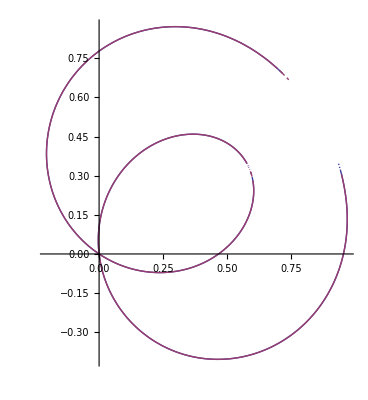

```mathematica
plboostk=ParametricPlot[{{vp Cos[alpha],vp Sin[alpha]},{vm Cos[alpha],vm Sin[alpha]}},{alpha,0,2*Pi}]
```

```mathematica
v3p
v3m
v1p
v1m
```

0.777299332309742+0. ⅈ

0.10388476105682+0. ⅈ

0.9541328971528

0.46660423791815

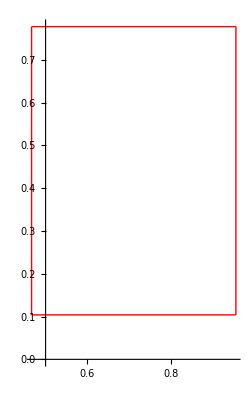

```mathematica
plotvpm=ParametricPlot[{{v1m,v3m+(v3p-v3m)t},{v1p,v3m+(v3p-v3m)t},{v1m+(v1p-v1m)t,v3m},{v1m+(v1p-v1m)t,v3p}},{t,0,1},PlotStyle->{RGBColor[1,0,0]}]
```

```mathematica
alphamaxes=FindRoot[D[vp Cos[alpha],alpha]==0,{alpha,{-1,1}}]
```

{alpha→{-1.51164+3.31067×10^-18 ⅈ,0.135969+1.74727×10^-14 ⅈ}}

```mathematica
alphamaxes=FindRoot[vp Cos[alpha]==0,{alpha,{-1,1}}]
```

{alpha→{-1.45267-5.25624×10^-18 ⅈ,1.5708-6.39565×10^-42 ⅈ}}

```mathematica
alphamaxes[[1,2,2]]
```

1.5708-6.39565×10^-42 ⅈ

```mathematica
(* Comoving wave vector *)
kfld=kfl*{-vphase Sqrt[-gcov[[1,1]]],Cos[alpha] Sqrt[gcov[[2,2]]],0,Sin[alpha] Sqrt[gcov[[4,4]]]}/.consts;
kflu=Table[Sum[gcon[[ii,jj]]*kfld[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost uu to the fluid frame *)
uflu= LorentzBoostUpper[uu,uu,ud,wu,wd];
ufld=LorentzBoostLower[ud,uu,ud,wu,wd];

(* Boost bu to the fluid frame *)
bflu=LorentzBoostUpper[bu,uu,ud,wu,wd];
bfld=LorentzBoostLower[bd,uu,ud,wu,wd];

wfl=-(kfld.uflu)//.consts
ksq=(kfld.kflu+wfl^2)//.consts
kdotva=kfld.bflu/Sqrt[EF]//.consts
kdotva2=kdotva^2
```

1. kfl vphase+0. kfl Cos[alpha]+0. kfl Sin[alpha]

-1. kfl^2 vphase^2+1. kfl^2 Cos[alpha]^2+1. kfl^2 Sin[alpha]^2+(1. kfl vphase+0. kfl Cos[alpha]+0. kfl Sin[alpha])^2

0.4841229182759271106474082 (0. kfl vphase-0.373307246021862001050416 kfl Cos[alpha]+1.787168869073136667620322 kfl Sin[alpha])

0.234375 (0. kfl vphase-0.373307246021862001050416 kfl Cos[alpha]+1.787168869073136667620322 kfl Sin[alpha])^2

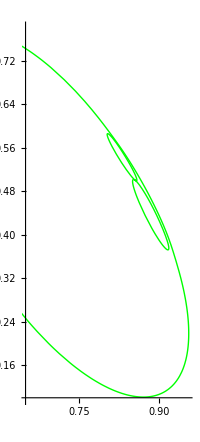

```mathematica
(* fast/slow modes *)
eq1x=0==(1/kfl^4*(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2));
eq1x=Rationalize[eq1x];

(* Create comoving wave 4-vel from wfl/kphys *)
Clear[vphase]
sols1x=Solve[eq1x,vphase];
absvp=sols1x[[4,1,2]];
absvm=sols1x[[1,1,2]];
vpphys={ 1, absvp Cos[alpha],0,absvp Sin[alpha]}//.consts;
vmphys={ 1, absvm Cos[alpha],0,absvm Sin[alpha]}//.consts;
upu=vel3p2vel4u[vpphys];
upd=Table[Sum[gcov[[ii,jj]]*upu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
umu=vel3p2vel4u[vmphys]; 
umd=Table[Sum[gcov[[ii,jj]]*umu[[ii]],{ii,1,4}],{jj,1,4}]//.consts;

(* Boost comoving wave 4-vel to the lab frame *)
uplabu=InverseLorentzBoostUpper[upu,uu,ud,wu,wd];
uplabd=InverseLorentzBoostLower[upd,uu,ud,wu,wd];

umlabu=InverseLorentzBoostUpper[umu,uu,ud,wu,wd];
umlabd=InverseLorentzBoostLower[umd,uu,ud,wu,wd];

(* physical 4-velocity *)
uplabphys= {uplabu[[1]] Sqrt[-gcov[[1,1]]],uplabu[[2]] Sqrt[gcov[[2,2]]],uplabu[[3]] Sqrt[gcov[[3,3]]],uplabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

umlabphys= {umlabu[[1]] Sqrt[-gcov[[1,1]]],umlabu[[2]] Sqrt[gcov[[2,2]]],umlabu[[3]] Sqrt[gcov[[3,3]]],umlabu[[4]] Sqrt[gcov[[4,4]]]}//.consts;

(* physical 3-velocity, vphys = uphys/uphyst *)
vplabphys =uplabphys/uplabphys[[1]];
vmlabphys =umlabphys/umlabphys[[1]];

(* r-phi plane *)
plboostu=ParametricPlot[{{vplabphys[[2]],vplabphys[[4]]},{vmlabphys[[2]],vmlabphys[[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,0]}]
```

```mathematica
sols1x//.consts/.alpha->0
sols1x//.consts/.alpha->Pi/2
absvp//.consts/.alpha->0
absvp//.consts/.alpha->Pi/2
```

{{vphase→-0.1462043369783847721587},{vphase→0.1462043369783847721587},{vphase→-0.95368986169150027422446},{vphase→0.95368986169150027422446}}

{{vphase→-0.7462197924622687644012},{vphase→0.7462197924622687644012},{vphase→-0.89454013063785631229768},{vphase→0.89454013063785631229768}}

0.95368986169150027422446

0.89454013063785631229768

```mathematica
(* WORK OUT GROUP 4-VELOCITY *)
```

```mathematica
dogroup=1;
```

```mathematica
If[dogroup==1,
Clear[omegalab,k1lab,k2lab,k3lab];
klabd={omegalab,k1lab,k2lab,k3lab}/.consts;
klabu=Table[Sum[gcon[[ii,jj]]*klabd[[ii]],{ii,1,4}],{jj,1,4}]//.consts;
wfl=-(klabd.uu)//.consts;
ksq=(klabd.klabu+wfl^2)//.consts;
kdotva=klabd.bu/Sqrt[EF]//.consts;
kdotva2=kdotva^2;
Disp=(wfl^4-wfl^2*(ksq*cms2+cs2*kdotva2)+ksq*cs2*kdotva2);
dxdlambdaconraw={D[Disp,klabd[[1]]],D[Disp,klabd[[2]]],D[Disp,klabd[[3]]],D[Disp,klabd[[4]]]};
omegalab = kd[[1]];
k1lab=kd[[2]];
k2lab=kd[[3]];
k3lab=kd[[4]];
vphasesols=Solve[Disp==0,vphase];
dxdlambdacon1=dxdlambdaconraw//.vphasesols[[1]];
dxdlambdacon2=dxdlambdaconraw//.vphasesols[[2]];
dxdlambdacon3=dxdlambdaconraw//.vphasesols[[3]];
dxdlambdacon4=dxdlambdaconraw//.vphasesols[[4]];
dxdlambdacon={dxdlambdacon1,dxdlambdacon2,dxdlambdacon3,dxdlambdacon4};
vphasecon = {vphasesols[[1]][[1]][[2]],vphasesols[[2]][[1]][[2]],vphasesols[[3]][[1]][[2]],vphasesols[[4]][[1]][[2]]};
];
```

```mathematica
dxdlambdacon//.{alpha->0,k->1}
```

{{27.56783908,8.575513696,0.00004654423093,2.477545183},{-1.6363655983,-0.89376974955,-0.000015753357442,-0.12656800274},{0.594480867,0.362894038,-0.0000124841172,0.0313948111},{-0.903094609,-0.574448184,-7.97578836×10^-6,-0.027105018}}

```mathematica
If[dogroup==1,
dxdlambdasq=dxdlambdacon*0;
vgroupcon=dxdlambdacon*0;
test=dxdlambdacon*0;
v3group=dxdlambdacon*0;
v3grouportho=dxdlambdacon*0;
v3grouporthoproj=dxdlambdacon*0;
v3phaseortho=dxdlambdacon*0;

(* choose direction for projection in lab frame to be same as Sasha choice *)
eprojcov=(kd)//.{alpha->beta}//.consts;
eprojcov[[1]]=0;
eprojcon=Table[Sum[eprojcov[[i]]*gcon[[i,j]],{i,1,4}],{j,1,4}]//.consts;
eprojcovnormalized=FullSimplify[eprojcov/Sqrt[eprojcov.eprojcon],{k>0}];

For[ii=1,ii≤4,ii++,
(* below should be -1 once normalized *)
dxdlambdasq[[ii]] = Sum[dxdlambdacon[[ii]][[i]]*dxdlambdacon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;
vgroupcon[[ii]] = dxdlambdacon[[ii]]/Sqrt[-dxdlambdasq[[ii]]];
(* below should give -1 always *)
test[[ii]]=Sum[vgroupcon[[ii]][[i]]*vgroupcon[[ii]][[j]]*gcov[[i,j]],{i,1,4},{j,1,4}]//.consts;
(* obtain 3-velocity, defines frame! *)
v3group[[ii]]=vgroupcon[[ii]]/vgroupcon[[ii]][[1]];
v3grouportho[[ii]]=Table[v3group[[ii]][[i]]*Sqrt[-gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;
(* normalized projection *)
v3grouporthoproj[[ii]]=Sum[v3grouportho[[ii]][[i]]*eprojcovnormalized[[i]],{i,1,4}];
v3phase2=vphasecon[[ii]]*Cos[alpha];
v3phase4=vphasecon[[ii]]*Sin[alpha];
myv3phase={1,v3phase2,0,v3phase4};
v3phaseortho[[ii]]=Table[myv3phase[[i]]*Sqrt[-gcov[[i,i]]/gcov[[1,1]]],{i,1,4}]//.consts;
Print[ii];
];
];
```

1

2

3

4

```mathematica
(* see if -1  for particular case since now FullSimplify takes too long *)
test//.{alpha->0,k->1}
```

{-1.,-1.,-1.,-1.}

```mathematica
(* ensure independent of magnitude of k *)
(v3grouportho//.{k->1,alpha->0})-(v3grouportho//.{k->2,alpha->0})
```

{{0. ⅈ,0.,0.,0.},{0. ⅈ,0.,0.,0.},{0. ⅈ,0.,0.,0.},{0. ⅈ,0.,0.,0.}}

```mathematica
(* prepare for plotting: k magnitude doesn't matter and choose beta=alpha for now *)
v3grouporthotoplot=Re[v3grouportho//.{k->1}];
v3phaseorthotoplot=Re[v3phaseortho//.{k->1}];
v3grouporthotoplotim=Im[v3grouportho//.{k->1}];
```

```mathematica
v3grouporthotoplot//.{alpha->Pi/4}
```

{{0,0.68761097,0.0000463132491,0.20728828},{0,0.914355896,-0.000118349706,0.388337163},{0,0.8203311,0.000080296834,0.5678487},{0,0.7333849,-0.00001452876,0.6739504}}

```mathematica
v3phaseorthotoplot//.{alpha->Pi/4}
```

{{0,0.82201744984,0,19.728418796},{0,1.19659998242,0,28.7183995781},{0,1.275124653,0,30.60299166},{0,1.292720071,0,31.02528171}}

```mathematica
(*
plv3groupim=ParametricPlot[{{v3grouporthotoplotim[[1]][[2]],v3grouporthotoplotim[[1]][[4]]},{v3grouporthotoplotim[[2]][[2]],v3grouporthotoplotim[[2]][[4]]},{v3grouporthotoplotim[[3]][[2]],v3grouporthotoplotim[[3]][[4]]},{v3grouporthotoplotim[[4]][[2]],v3grouporthotoplotim[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,1]},PlotPoints->10]
*)
```

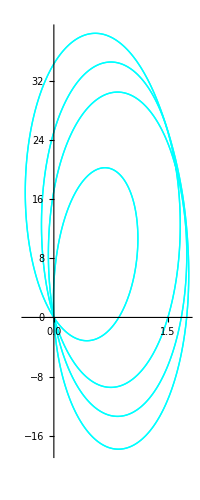

```mathematica
plv3phase=ParametricPlot[{{v3phaseorthotoplot[[1]][[2]],v3phaseorthotoplot[[1]][[4]]},{v3phaseorthotoplot[[2]][[2]],v3phaseorthotoplot[[2]][[4]]},{v3phaseorthotoplot[[3]][[2]],v3phaseorthotoplot[[3]][[4]]},{v3phaseorthotoplot[[4]][[2]],v3phaseorthotoplot[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,1]},PlotPoints->100]
```

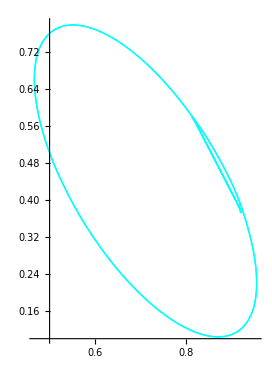

```mathematica
(* r-phi plane for the full quartic solution *)
plv3group=ParametricPlot[{{v3grouporthotoplot[[1]][[2]],v3grouporthotoplot[[1]][[4]]},{v3grouporthotoplot[[2]][[2]],v3grouporthotoplot[[2]][[4]]},{v3grouporthotoplot[[3]][[2]],v3grouporthotoplot[[3]][[4]]},{v3grouporthotoplot[[4]][[2]],v3grouporthotoplot[[4]][[4]]}},{alpha,0,2*Pi},PlotStyle->{RGBColor[0,1,1]},PlotPoints->100]
```

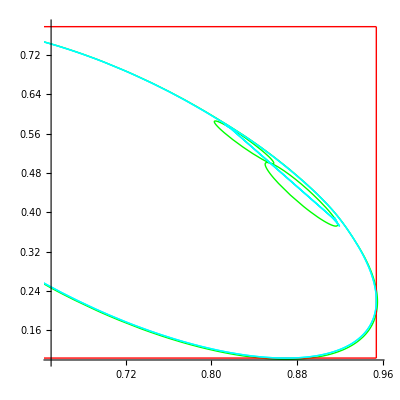

figzoom1.eps

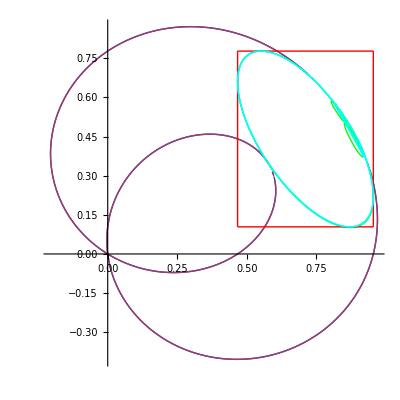

fig1.eps

```mathematica
figzoom=Show[plboostu,plotvpm,plv3group,AspectRatio->1]
Export["figzoom1.eps",figzoom]
fig=Show[plboostk,plboostu,plotvpm,plv3group,AspectRatio->1]
Export["fig1.eps",fig]
```

```mathematica
(* Done *)
```

```mathematica
cms2
cs2
va2
```

0.911458333333333333333333

0.59523809523809523809523809524

0.78125